```mathematica
Clear["Global`*"]
```

### Gaussian quadrature for triangle, imported from “Quadrature Formulas in Two Dimensions Math 5172 - Finite Element Method Section 001, Spring 2010”

```mathematica
(*first two columns give ξ and η, third column gives the weights. *)
ξ5={0.33333333333333,0.47014206410511,0.47014206410511,0.05971587178977,0.10128650732346,0.10128650732346,0.79742698535309};
η5={0.33333333333333,
0.47014206410511,
0.05971587178977,
0.47014206410511,
0.10128650732346,
0.79742698535309,
0.10128650732346};
w5={0.22500000000000,
0.13239415278851,
0.13239415278851,
0.13239415278851,
0.12593918054483,
0.12593918054483,
0.12593918054483};
```

```mathematica
ξ6={0.24928674517091,
0.24928674517091,
0.50142650965818,
0.06308901449150,
0.06308901449150,
0.87382197101700,
0.31035245103378,
0.63650249912140,
0.05314504984482,
0.63650249912140,
0.31035245103378,
0.05314504984482};
η6={0.24928674517091,
0.50142650965818,
0.24928674517091,
0.06308901449150,
0.87382197101700,
0.06308901449150,
0.63650249912140,
0.05314504984482,
0.31035245103378,
0.31035245103378,
0.05314504984482,
0.63650249912140};
w6={0.11678627572638,
0.11678627572638,
0.11678627572638,
0.05084490637021,
0.05084490637021,
0.05084490637021,
0.08285107561837,
0.08285107561837,
0.08285107561837,
0.08285107561837,
0.08285107561837,
0.08285107561837};
```

```mathematica
ξ7={0.33333333333333,
0.26034596607904,
0.26034596607904,
0.47930806784192,
0.06513010290222,
0.06513010290222,
0.86973979419557,
0.31286549600487,
0.63844418856981,
0.04869031542532,
0.63844418856981,
0.31286549600487,
0.04869031542532};
η7={0.33333333333333,
0.26034596607904,
0.47930806784192,
0.26034596607904,
0.06513010290222,
0.86973979419557,
0.06513010290222,
0.63844418856981,
0.04869031542532,
0.31286549600487,
0.31286549600487,
0.04869031542532,
0.63844418856981};
w7={-0.14957004446768,
0.17561525743321,
0.17561525743321,
0.17561525743321,
0.05334723560884,
0.05334723560884,
0.05334723560884,
0.07711376089026,
0.07711376089026,
0.07711376089026,
0.07711376089026,
0.07711376089026,
0.07711376089026};
```

```mathematica
ξ8={0.33333333333333,
0.45929258829272,
0.45929258829272,
0.08141482341455,
0.17056930775176,
0.17056930775176,
0.65886138449648,
0.05054722831703,
0.05054722831703,
0.89890554336594,
0.26311282963464,
0.72849239295540,
0.00839477740996,
0.72849239295540,
0.26311282963464,
0.00839477740996};
η8={0.33333333333333,
0.45929258829272,
0.08141482341455,
0.45929258829272,
0.17056930775176,
0.65886138449648,
0.17056930775176,
0.05054722831703,
0.89890554336594,
0.05054722831703,
0.72849239295540,
0.00839477740996,
0.26311282963464,
0.26311282963464,
0.00839477740996,
0.72849239295540};
w8={0.14431560767779,
0.09509163426728,
0.09509163426728,
0.09509163426728,
0.10321737053472,
0.10321737053472,
0.10321737053472,
0.03245849762320,
0.03245849762320,
0.03245849762320,
0.02723031417443,
0.02723031417443,
0.02723031417443,
0.02723031417443,
0.02723031417443,
0.02723031417443};
```

```mathematica
fTest[x_,y_]:=Cos[x]Sin[y^2];
```

```mathematica
NIntegrate[fTest[x,y],{x,0,1},{y,0,1-x}]
```

0.0777232

```mathematica
(1/2∑_(k=1)^(Length@w5) w5[[k]] fTest[ξ5[[k]],η5[[k]]])
```

0.077723

```mathematica
(1/2∑_(k=1)^(Length@w6) w6[[k]] fTest[ξ6[[k]],η6[[k]]])
```

0.077723

```mathematica
(1/2∑_(k=1)^(Length@w7) w7[[k]] fTest[ξ7[[k]],η7[[k]]])
```

0.0777227

```mathematica
(1/2∑_(k=1)^(Length@w8) w8[[k]] fTest[ξ8[[k]],η8[[k]]])
```

0.0777232

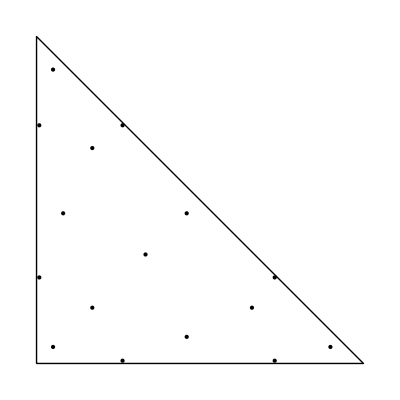

```mathematica
Graphics[{Line[{{0,0},{1,0},{0,1},{0,0}}],Point[Transpose[{ξ8,η8}]]}]
```

### Export the weights and nodes to files in the form (ξ, η, w):

```mathematica
dat5=Table[{ξ5[[q]],η5[[q]],w5[[q]]},{q,1,Length@w5}];
Export["./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p5.txt",dat5,"Table"]
```

./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p5.txt

```mathematica
dat6=Table[{ξ6[[q]],η6[[q]],w6[[q]]},{q,1,Length@w6}];
Export["./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p6.txt",dat6,"Table"]
```

./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p6.txt

```mathematica
dat7=Table[{ξ7[[q]],η7[[q]],w7[[q]]},{q,1,Length@w7}];
Export["./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p7.txt",dat7,"Table"]
```

./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p7.txt

```mathematica
dat8=Table[{ξ8[[q]],η8[[q]],w8[[q]]},{q,1,Length@w8}];
Export["./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p8.txt",dat8,"Table"]
```

./Desktop/PhDWork/year1/BIMCodes/Headers/triangleQuadratures/p8.txt